# Learning tabular data

```mathematica
Get["neural-logic.m",Path->SetDirectory[ParentDirectory[NotebookDirectory[]]<>"/prototype"]]
```

```mathematica
?neurallogic`*
```

## Get data

```mathematica
data=ResourceData["663653b1-6151-48ad-b693-3ee813b191c6"]
```

Dataset[<>]

```mathematica
{trainData,testData}=[data,"TestSetSize"->Scaled[0.2],"Shuffle"->True];
```

## Create feature encoders

```mathematica
Encoders[data_]:=Block[{features=Normal[Keys@First[data]],featureValues},
featureValues={#,Normal[DeleteDuplicates[data[All,#]]]}&/@features;
Association[First[#]->NetEncoder[{"Class",Last[#],"IndicatorVector"}]&/@featureValues]
]
encoders=Encoders[trainData];
inputSize=Total[First[#["Output"]]&/@Normal/@Values[Drop[encoders,-1]]];
classes=Normal[DeleteDuplicates[data[All,"Acceptability"]]];
```

```mathematica
featureLayer=NetGraph[<|"Catenate"->CatenateLayer[]|>,
Map[NetPort[First[#]]->"Catenate"&,Drop[Normal[encoders],-1]],
"PurchasePrice"->encoders["PurchasePrice"],
"MaintenanceCost"->encoders["MaintenanceCost"],
"Doors"->encoders["Doors"],
"Passengers"->encoders["Passengers"],
"Cargo"->encoders["Cargo"],
"Safety"->encoders["Safety"]
];
```

## Create net

```mathematica
{softNet,hardNet}=Block[{numClasses=Length[classes],classificationLayerSize},
classificationLayerSize=128*numClasses;
HardNeuralChain[{
HardNeuralNAND[inputSize,classificationLayerSize,RandomBalancedNormalSoftBits[#]&,RandomBalancedNormalSoftBits[#]&],
HardNeuralReshapeLayer[classificationLayerSize,numClasses]
}]];
```

```mathematica
net=NetGraph[<|"FeatureLayer"->featureLayer,"SoftNet"->softNet|>,{"FeatureLayer"->"SoftNet"}];
```

```mathematica
trainableNet=NetGraph[
<|"Net"->net,"Loss"->HardClassificationLoss[]|>,
{NetPort["Acceptability"]->NetPort["Loss","Target"],"Net"->"Loss"},
"Acceptability"->encoders["Acceptability"]
];
```

```mathematica
NetFlatten[trainableNet]
```

NetGraph[<>]

## Train net

```mathematica
result=NetTrain[trainableNet,trainData,All,
ValidationSet->testData,
LossFunction->"Loss",
Method->{"ADAM"},
BatchSize->Automatic,
TargetDevice->"GPU",
MaxTrainingRounds->20000];
```

## Evaluate soft net

```mathematica
NetExtract[result["TrainedNet"],{"Net","SoftNet",1,1,"Weights"}]
```

NetGraph[<>]

```mathematica
NetInsertSharedArrays[result["TrainedNet"]]
```

NetGraph[<>]

```mathematica
NetExtract[NetInsertSharedArrays[result["TrainedNet"]],NetArray[All]]
```

NetGraph[<>]

```mathematica
trainedSoftNet=NetGraph[
<|"TrainedNet"->NetDelete[NetFlatten[result["TrainedNet"]],"Loss/Error"]|>,
{},"Output"->NetDecoder[encoders["Acceptability"]]
];
```

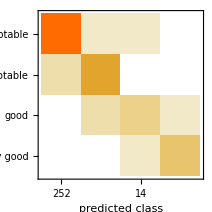
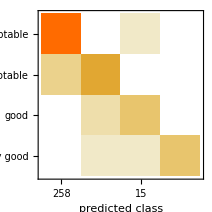
{Classifier Measurements
Classifier method | Net
Number of test examples | 346
Accuracy | (97.10.9) %
Accuracy baseline | (72.52.4) %
Geometric mean of probabilities | 0.891 ± 0.028
Mean cross entropy | 0.115 ± 0.032
Single evaluation time | 4.7 ms/example
Batch evaluation speed | 2.94 examples/ms
-Graphics- | ,Classifier Measurements
Classifier method | Net
Number of test examples | 346
Accuracy | (96.01.1) %
Accuracy baseline | (72.52.4) %
Geometric mean of probabilities | 0.899 ± 0.02
Mean cross entropy | 0.106 ± 0.022
Single evaluation time | 4.73 ms/example
Batch evaluation speed | 1.75 examples/ms
-Graphics- | }

```mathematica
ClassifierMeasurements[#,testData->"Acceptability"]&/@{trainedSoftNet,HardNet[trainedSoftNet]}
```

```mathematica
trainedSoftNet
```

NetGraph[<>]

```mathematica
ConvertRandomWeightsToDeterministicWeights[]
```

```mathematica
GetNetArrays[trainedSoftNet]
```

<|TrainedNet/Net/SoftNet/1→NetArrayLayer[<>],TrainedNet/Net/SoftNet/2→NetArrayLayer[<>],TrainedNet/Net/SoftNet/4→NetArrayLayer[<>],TrainedNet/Net/SoftNet/5→NetArrayLayer[<>]|>

## Evaluate hard net

```mathematica
hnf=HardNetFunction[hardNet,trainedSoftNet];
```

```mathematica
hncwt=HardNetClassify[hnf,featureLayer,NetDecoder[encoders["Acceptability"]],testData,"Acceptability"];
eval=HardNetClassifyEvaluation[hncwt]
```

<|Accuracy→0.,Results→<|<|Prediction→First[$Failed],Target→unacceptable|>→251,<|Prediction→First[$Failed],Target→acceptable|>→64,<|Prediction→First[$Failed],Target→good|>→16,<|Prediction→First[$Failed],Target→very good|>→15|>|>

```mathematica
hncwt2=Block[{trainedHardNet=HardNet[trainedSoftNet]},
Association[{"Prediction"->trainedHardNet[KeyDrop[{"Acceptability"}]@#],"Target"->#["Acceptability"]}]&/@Normal[testData]
];
eval2=HardNetClassifyEvaluation[hncwt2]
```

<|Accuracy→0.965318,Results→<|<|Prediction→unacceptable,Target→unacceptable|>→247,<|Prediction→acceptable,Target→acceptable|>→59,<|Prediction→good,Target→good|>→16,<|Prediction→very good,Target→very good|>→12,<|Prediction→good,Target→very good|>→3,<|Prediction→good,Target→acceptable|>→3,<|Prediction→acceptable,Target→unacceptable|>→3,<|Prediction→good,Target→unacceptable|>→1,<|Prediction→very good,Target→acceptable|>→1,<|Prediction→unacceptable,Target→acceptable|>→1|>|>

```mathematica
Quantity[Length[Flatten[ExtractWeights[trainedSoftNet]]]/8/1024//N,"Kilobytes"]
```

1.3125 kB

```mathematica
HardNetBooleanExpression[hnf,inputSize];
```

## Train standard net

```mathematica
classifier=Classify[trainData->"Acceptability",Method->"NeuralNetwork",PerformanceGoal->"Memory"]
```

ClassifierFunction[…]

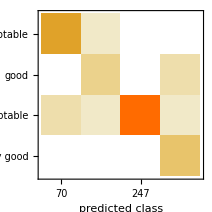
Classifier Measurements
Classifier method | NeuralNetwork
Number of test examples | 346
Accuracy | (98.00.8) %
Accuracy baseline | (72.52.4) %
Geometric mean of probabilities | 0.931 ± 0.017
Mean cross entropy | 0.0714 ± 0.018
Single evaluation time | 5.82 ms/example
Batch evaluation speed | 1.47 examples/ms
-Graphics- |

```mathematica
measurements=ClassifierMeasurements[classifier,testData->"Acceptability"]
```

```mathematica
Information[classifier,"FunctionMemory"]
```

357. kB

## Notes

```mathematica
softWeights=Flatten[ExtractWeights[trainedSoftNet]];
```

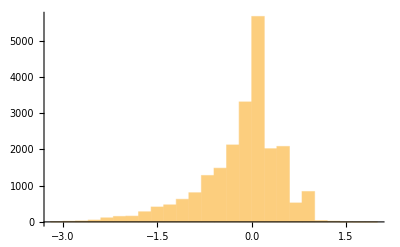

```mathematica
Histogram[softWeights,PlotRange->All]
```